# Infinite 3D medium, Isotropic Point Source, Linearly-Anisotropic Scattering

## Exponential Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

-Graphics-

c - single-scattering albedo
Σt - extinction coefficient
r - radial position coordinate in medium (distance from point source at origin)
u = cos θ - direction cosine
b - anisotropy parameter

### Namespace

```mathematica
Begin["inf3Disopointlinanisoscatter`"]
```

inf3Disopointlinanisoscatter`

## Util

```mathematica
SA[d_,r_]:=d Pi^(d/2)/Gamma[d/2+1] r^(d-1)
```

### Diffusion modes

```mathematica
diffusionMode[v_,d_,r_]:=(2 π)^(-d/2) r^(1-d/2) v^(-1-d/2) BesselK[1/2 (-2+d),r/v]
```

### Fluence: exact solution

```mathematica
Alinearaniso[c0_,g_,v_]:=(v(1-v^2))/(c0(v^2-1+c0+3g(1-c0)(3-c0-3(1-c0)(1-g c0)/v^2)));
glinearaniso[c0_,g_,u_]:=1/(((Pi c0 u)/2(1+3 g(1-c0)u^2))^2+(1+3 g c0(1-c0)u^2-(1+3 g(1-c0)u^2)c0/2 u Log[(1+u)/(1-u)])^2);
v0linearaniso[c_,g_]:=ReplaceAll[Abs[v],FindRoot[1+(3 g c(1-c))/v^2-(1+(3 g(1-c))/v^2)c/(2v)Log[(1+v)/(1-v)],{v,1.1}]];
```

```mathematica
ϕexact[r_,Σt_,c_,b_]:=(# Σt)/(2 Pi r)Alinearaniso[c,b/3,#]Exp[-# r Σt]+Σt/(4 Pi r)NIntegrate[1/u^2 glinearaniso[c,b/3,u]Exp[-Σt r/u],{u,0,1}]&[v0linearaniso[c,b/3]]
```

### Fluence: Rigorous Diffusion Approximation

```mathematica
ϕrigourousDiffusion[r_,Σt_,c_,b_]:=(# Σt)/(2 Pi r)Alinearaniso[c,b/3,#]Exp[-# r Σt]&[v0linearaniso[c,b/3]]
```

### Fluence: Classical Diffusion Approximation

```mathematica
ϕDiffusion[r_,Σt_,c_,b_]:=(ⅇ^(-r √((1-c) (3-b c)) Σt) (3-b c) Σt)/(4 π r)
```

### Fluence: Grosjean Modified Diffusion Approximation

```mathematica
ϕGrosjean[r_,Σt_,c_,b_]:=E^(-r Σt)/(4 Pi r^2)+c/(1-c)1/Σt diffusionMode[1/(√3 √(((c-1) (-3+b c))/(6+b (-1+c)^2-3 c)) Σt),3,r]
```

```mathematica
Clear[a,b,c,Σt,r];FullSimplify[inf3Disopointlinanisoscatter`ϕGrosjean[r,Σt,c,b],Assumptions->Σt>0&&0<c<1&&b>-1&&b<1]
```

(ⅇ^(-r Σt)-(3 c (-3+b c) ⅇ^(-√3 √(((-1+c) (-3+b c))/(6+b (-1+c)^2-3 c)) r Σt) r Σt)/(6+b (-1+c)^2-3 c))/(4 π r^2)

### Nth-collided fluence - Gaussian approximation

```mathematica
twomomentGaussian[r_,m0_,m2_]:=(3 √(3/2) ⅇ^(-(3 m0 r^2)/(2 m2)) m0^(5/2))/(2 m2^(3/2) π^(3/2))
```

```mathematica
ϕGaussian[r_,Σt_,c_,b_,n_]:=twomomentGaussian[r,c^n/Σt,(2 3^-n (b^(2+n)+3^(2+n) (1+n)-3^(1+n) b (2+n)) c^n)/((-3+b)^2 Σt^3)]
```

## load MC data

```mathematica
ppoints[xs_,dr_,maxx_]:=Table[{dr(i)-0.5dr,xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
ppointsu[xs_,du_,Σt_]:=Table[{-1.0 +du(i)-0.5du,xs[[i]]/(2Σt)},{i,1,Length[xs]}][[1;;-1]]
```

```mathematica
fs=FileNames["code/3D_medium/infinite3Dmedium/Isotropicpointsource/MCdata/inf3D_isotropicpoint_linanisoscatter*"];
```

```mathematica
index[x_]:=Module[{data,c,mfp,b},
data=Import[x,"Table"];
mfp=data[[1,13]];
c=data[[2,3]];
b=data[[1,16]];
{c,mfp,b,data}];
simulations=index/@fs;
cs=Union[#[[1]]&/@simulations]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,0.999}

```mathematica
mfps=Union[#[[2]]&/@simulations]
```

{0.3,1}

```mathematica
bs=Union[#[[3]]&/@simulations]
```

{-0.9,0.7}

```mathematica
numcollorders=inf3Disopointlinanisoscatter`simulations[[1]][[-1]][[2,13]];
```

## Compare Deterministic and MC

### Mean Track Length

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set b","b = "<>ToString[#]:>(b=#;)&/@bs],Dynamic[b]}}
```

{{Set c,},{Set mfp,},{Set b,}}

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&&#[[3]]==b&][[4]];
meanTL=data[[-1]]
mfp/(1-c)
```

{Mean,track,length:,1.42865}

1.42857

### Fluence - Exact solution comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set b","b = "<>ToString[#]:>(b=#;)&/@bs],Dynamic[b]}}
```

{{Set c,},{Set mfp,},{Set b,}}

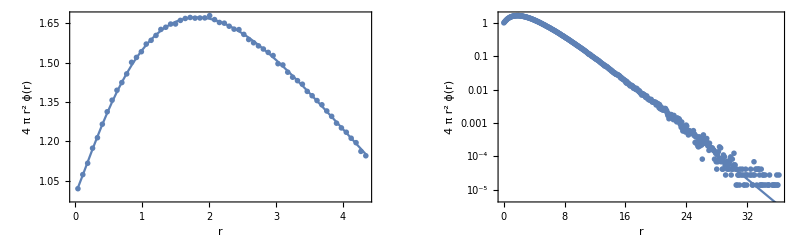

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&&#[[3]]==b&][[4]];
maxr=data[[2,5]];
dr=data[[2,7]];
pointsFluence=ppoints[data[[6]],dr,maxr];
exact1FluenceShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact[#[[1]],1/mfp,c,b]}]& /@pointsFluence[[1;;60]];
exact1Fluence=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact[#[[1]],1/mfp,c,b]}]& /@pointsFluence[[1;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1FluenceShallow,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1Fluence,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution\nInfinite 3D, isotropic point source, linearly-anisotropic scattering, fluence ϕ[r], c = "<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]<>", b = "<>ToString[b]]
```

### Fluence - Diffusion Approximations

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set b","b = "<>ToString[#]:>(b=#;)&/@bs],Dynamic[b]}}
```

{{Set c,},{Set mfp,},{Set b,}}

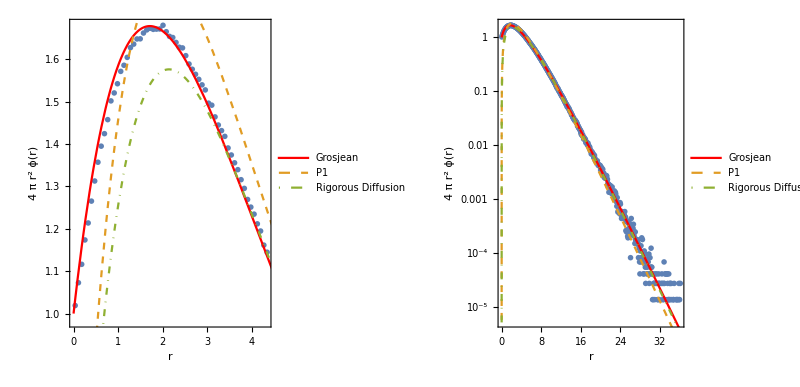

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&&#[[3]]==b&][[4]];
maxr=data[[2,5]];
dr=data[[2,7]];
pointsFluence=ppoints[data[[6]],dr,maxr];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[{
4 Pi r^2 ϕGrosjean[r,1/mfp,c,b],
4 Pi r^2  ϕDiffusion[r,1/mfp,c,b],
4 Pi r^2  ϕrigourousDiffusion[r,1/mfp,c,b]
}
,{r,0,maxr},PlotRange->All,PlotStyle->{Red,Dashed,DotDashed},PlotLegends->Placed[{"Grosjean","P1","Rigorous Diffusion"},{0.5,.2}]],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence,PlotRange->All,PlotStyle->PointSize[.01]],
LogPlot[{
4 Pi r^2 ϕGrosjean[r,1/mfp,c,b],
4 Pi r^2  ϕDiffusion[r,1/mfp,c,b],
4 Pi r^2  ϕrigourousDiffusion[r,1/mfp,c,b]
}
,{r,0,maxr},PlotRange->All,PlotStyle->{Red,Dashed,DotDashed},PlotLegends->Placed[{"Grosjean","P1","Rigorous Diffusion"},{0.3,.2}]],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Diffusion Approximations vs MC\nInfinite 3D, isotropic point source, linearly-anisotropic scattering, fluence ϕ[r], c = "<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]<>", b = "<>ToString[b]]
```

### N-th collided Fluence - Approximations

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set collision order","collisionOrder = "<>ToString[#]:>(collisionOrder=#;)&/@Range[0,numcollorders-1]],Dynamic[collisionOrder]},
{ActionMenu["Set b","b = "<>ToString[#]:>(b=#;)&/@bs],Dynamic[b]}}
```

{{Set c,},{Set mfp,},{Set collision order,},{Set b,}}

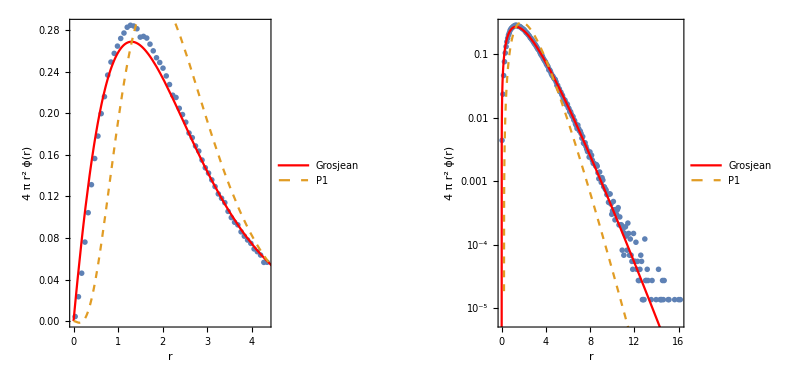

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&&#[[3]]==b&][[4]];
maxr=data[[2,5]];
dr=data[[2,7]];
fluencei=3 numcollorders+15+collisionOrder;

pointsFluence=ppoints[data[[fluencei]],dr,maxr];
seriesclassical=c^collisionOrder SeriesCoefficient[ϕDiffusion[r,1/mfp,C,b],{C,0,collisionOrder}];
seriesG=c^collisionOrder SeriesCoefficient[ϕGrosjean[r,1/mfp,C,b],{C,0,collisionOrder}];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[{4 Pi r^2 seriesG,4 Pi r^2 seriesclassical},{r,0,maxr},PlotRange->All,PlotStyle->{Red,Dashed},PlotLegends->Placed[{"Grosjean","P1"},{0.5,.2}]],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence,PlotRange->All,PlotStyle->PointSize[.01]],
LogPlot[{4 Pi r^2 seriesG,4 Pi r^2 seriesclassical},{r,0,maxr},PlotRange->All,PlotStyle->{Red,Dashed},PlotLegends->Placed[{"Grosjean","P1"},{0.5,.2}]],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Diffusion Approximations\nInfinite 3D medium, isotropic point source, linearly-anisotropic scattering, n-th scattered fluence ϕ[r|"<>ToString[collisionOrder]<>"], c ="<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]<>", b = "<>ToString[b]]
```

### Compare moments of ϕ

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set b","b = "<>ToString[#]:>(b=#;)&/@bs],Dynamic[b]}}
```

{{Set c,},{Set mfp,},{Set b,}}

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&&#[[3]]==b&][[4]];
nummoments=data[[2,15]];
ϕmoments=N[{data[[10]]}];
ks=Table[k,{k,0,nummoments-1}];
analytic={1/(1-c)mfp,0,-6/((c-1)^2(c b-3))mfp^3,0,mfp^5(24(4c-9))/((c-1)^3(c b - 3)^2)};
j=Join[{ks},{analytic},ϕmoments];

TableForm[
Join[{{"k","analytic","MC"}},Transpose[j]]
]
```

k | analytic | MC
0 | 10. | 10.0102
1 | 0 | 40.0563
2 | 253.165 | 254.167
3 | 0 | 2173.52
4 | 23073.2 | 23352.3

### Compare nth moments of C

2nd and 4th moments of the scalar collision rate density C(x) for the nth collision

```mathematica
C2moment[n_,c_,g_,mfp_]:=c^(n-1)(n (2 mfp^2)+g/(1-g)2 ( mfp^2) (n-(1-g^n)/(1-g)))
```

```mathematica
C4moment[n_,c_,b_,mfp_]:=c^(n-1)/mfp(1/(-3+b)^4 4 3^(1-n) mfp^5 (3^n (-6 b (36+(33+5 (-1+n)) (-1+n))+9 (18+5 (-1+n)) n+b^2 (28+5 (-1+n)) (2+n))+2 b^(1+n) (12 (2+n)+b (-36-13 (-1+n)+3 b n))))
```

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set b","b = "<>ToString[#]:>(b=#;)&/@bs],Dynamic[b]}}
```

{{Set c,},{Set mfp,},{Set b,}}

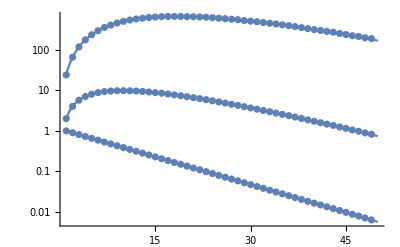

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&&#[[3]]==b&][[4]];
nummoments=data[[2,15]];
ϕmoments=data[[13;;13+numcollorders-2]];
Show[
ListLogPlot[#[[5]]&/@ϕmoments,PlotRange->All],
ListLogPlot[#[[3]]&/@ϕmoments,PlotRange->All],
ListLogPlot[#[[1]]&/@ϕmoments,PlotRange->All],
LogPlot[C2moment[n,c,b/3,mfp],{n,1,numcollorders},PlotRange->All],
LogPlot[C4moment[n,c,b,mfp],{n,1,numcollorders},PlotRange->All],
LogPlot[c^(n-1),{n,1,numcollorders},PlotRange->All],PlotRange->All
]
```

## Close namespace

```mathematica
End[]
```